```mathematica
data = Import["/net/home/f09/bajennissen/research/DAY189/sec_int_data/675nm.dat"]
```

{{1.63065,0.165006},{1.58758,0.164158},{1.51023,0.17823},{1.46132,0.185483},{1.41705,0.190786},{1.38078,0.193179},{1.34407,0.20872},{1.30453,0.205957},{1.27782,0.209612},{1.24828,0.206119},{1.22646,0.216723},{1.20042,0.223464},{1.183,0.221302},{1.16401,0.222423},{1.14739,0.215353},{1.13423,0.21793},{1.12389,0.216401},{1.11401,0.0146915},{1.10574,0.171598},{1.09905,0.139675},{1.09389,0.138544},{1.08918,0.199588},{1.08895,0.203838},{1.08874,0.200816},{1.08738,0.238072},{1.08767,0.241455},{1.08994,0.226976},{1.0948,0.239489},{1.10288,0.239096},{1.1168,0.243338},{1.12832,0.22058},{1.1517,0.240119},{1.18117,0.245062},{1.20042,0.238938},{1.25083,0.236573},{1.28067,0.22586},{1.3108,0.23815},{1.33715,0.223783}}

0.256954-0.0421427 x

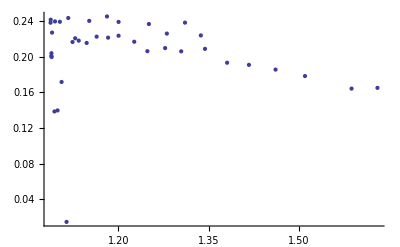

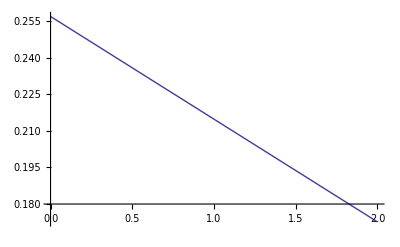

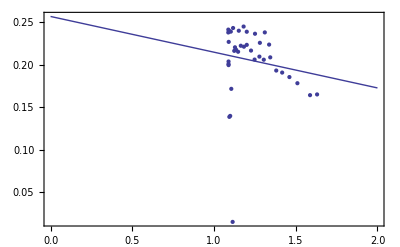

```mathematica
line = Fit[data,{1,x},x]
DataPlot=ListPlot[data]
FitPlot=Plot[line,{x,0,2}]
Show[DataPlot,FitPlot,PlotRange->All,Frame->True,AxesOrigin->{0,0}]
```